```mathematica
Clear["Global`*"]
```

```mathematica
CE1=t(s-Md^2)(s-Md^2-Mll^2+t)(Mll^4+6 Mll^2 t+t^2+4 m^2 Mll^2)+(Mll^2-t)^2(t^2 Mll^2+Md^2(Mll^2+t)^2+4 m^2 Md^2 Mll^2);
CE2=-t(s-Md^2)(s-Md^2-Mll^2+t)(Mll^4+t^2+4 m^2(Mll^2+2t-2 m^2))+(Mll^2-t)^2(-Md^2(Mll^4+t^2)+2 m^2(-t^2-2 Md^2 Mll^2+4 m^2 Md^2));
CM1=CE1-2 Md^2(1+τd)(Mll^2-t)^2(Mll^4+t^2+4 m^2 Mll^2);
CM2=CE2+2 Md^2(1+τd)(Mll^2-t)^2(Mll^4+t^2+4 m^2(Mll^4-t-2 m^2));
CM2/.{t->-1,Mll->√10,Eγ->8}
vCE1=Normal[Series[CE1,{t,0,1},{m,0,1},{Md,0,2}]];
vCE2=Normal[Series[CE2,{t,0,1},{m,0,1},{Md,0,2}]];
vCM1=Normal[Series[CM1,{t,0,1},{m,0,1},{Md,0,2}]];
vCM2=Normal[Series[CM2,{t,0,1},{m,0,1},{Md,0,2}]];
```

106720.

General::ivar: 0.000510999 is not a valid variable.

General::ivar: 1.8756 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.000510999 is not a valid variable.

General::ivar: 1.8756 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.000510999 is not a valid variable.

General::ivar: 1.8756 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: 0.000510999 is not a valid variable.

General::ivar: 1.8756 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
α=1/137;
m=0.000511;
Md=0.938*2;
β=√(1-4 m^2/Mll^2);
τd=-t/(4 Md^2);
s=Md^2+2Md Eγ;
```

```mathematica
CE=CE1+CE2/β Log[(1+β)/(1-β)];
CM=CM1+CM2/β Log[(1+β)/(1-β)];
vCE=vCE1+vCE2/β Log[(1+β)/(1-β)];
vCM=vCM1+vCM2/β Log[(1+β)/(1-β)];
```

```mathematica
dσdtdM2=(4 α^3 β)/((s-Md^2)^2 t^2(Mll^2-t)^4)(CE(GC[-t]^2+8/9 τd^2 GQ[-t]^2)+CM 2/3 τd GM[-t]^2);
dσdtdM2/.{t->-1,Eγ->8,Mll->√10}
vdσdtdM2=(4 α^3 β)/((s-Md^2)^2 t^2(Mll^2-t)^4)(vCE(GC^2+8/9 τd^2 GQ^2)+vCM 2/3 τd GM^2);
```

-3.6964×10^-12

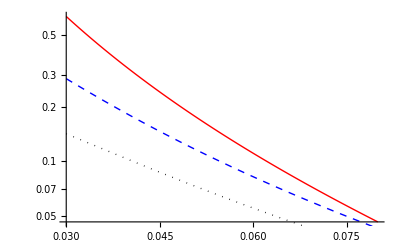

```mathematica
p1=LogPlot[dσdtdM2/.{GM->1,GC->0.627,GQ->47,Eγ->5,t->-0.01,Mll->√MLL},{MLL,0.03,0.08},PlotStyle->{Red,Thick}];
p2=LogPlot[dσdtdM2/.{GM->1,GC->0.627,GQ->47,Eγ->5,t->-0.02,Mll->√MLL},{MLL,0.03,0.08},PlotStyle->{Blue,Thick,Dashed}];
p3=LogPlot[dσdtdM2/.{GM->1,GC->0.627,GQ->47,Eγ->5,t->-0.03,Mll->√MLL},{MLL,0.03,0.08},PlotStyle->{Black,Thick,Dotted}];
Show[p1,p2,p3]
```